```mathematica
L=19;
sigmac = {0.529317561497303,0.162583867414539,0.05305242922289672,0.019876013692561836,0.007763262797399105,0.003057425282026672,0.0011586023627724214,0.00040520867304012775,0.00010889900010480069};
m = Table[(L+1)/2+i,{i,1,(L-1)/2,1}]
n = Table[(L+1)/2-i,{i,1,(L-1)/2,1}]
```

{11,12,13,14,15,16,17,18,19}

{9,8,7,6,5,4,3,2,1}

```mathematica
x= Pi*((m+1/2)/(L+2));
y = Pi*((n+1/2)/(L+2));
s = -Pi/2 +x
```

{π/21,(2 π)/21,π/7,(4 π)/21,(5 π)/21,(2 π)/7,π/3,(8 π)/21,(3 π)/7}

```mathematica
f[k_,a_]:= (((1/Sin[k* Pi/(L+2)])^(2*a)+(1/Sin[k* Pi/(L+2)])^(-2a))^(1/2))/(4Sin[Pi/2+(2k Pi)/(L+2)]Sin[Pi/2-(2k Pi)/(L+2)])^(a/2)
```

```mathematica
(L+2)(x-y)/Pi
```

{2,4,6,8,10,12,14,16,18}

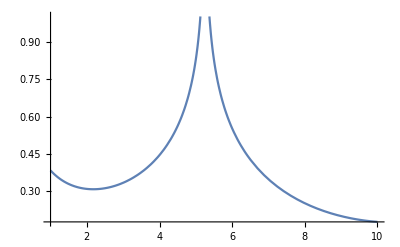

```mathematica
Plot[Log[f[k,1/4]],{k,1,10}]
```

```mathematica
N[(21/20)^(1/4),4]
```

1.012

```mathematica
0.305/0.3
```

1.01667